# Wishart Distribution

Generate a random positive definitive matrix to use as parameters for the Wishart distribution.

```mathematica
Σ=DiagonalMatrix[RandomReal[10,5]];
```

```mathematica
MatrixForm[Σ]
```

(7.98927 | 0. | 0. | 0. | 0.
0. | 5.41475 | 0. | 0. | 0.
0. | 0. | 1.45318 | 0. | 0.
0. | 0. | 0. | 5.7257 | 0.
0. | 0. | 0. | 0. | 0.843219)

Matrices from the Wishart distribution are symmetric and positive definite.

```mathematica
dist=WishartMatrixDistribution[30,Σ];
```

```mathematica
mat=RandomVariate[dist];
MatrixForm[mat]
```

(151.058 | 93.3738 | 15.7409 | -6.72645 | -10.975
93.3738 | 204.952 | 26.2171 | -13.3601 | 22.0374
15.7409 | 26.2171 | 33.5258 | 18.9332 | -3.66502
-6.72645 | -13.3601 | 18.9332 | 150.945 | -3.94175
-10.975 | 22.0374 | -3.66502 | -3.94175 | 30.2527)

```mathematica
SymmetricMatrixQ[mat]&&PositiveDefiniteMatrixQ[mat]
```

True

For any nonzero vector y  and Wishart matrix w  with scale matrix Σ, the statistic  is  y.w.y/(y.Σ.y)is χ^2 distributed

```mathematica
y=#/Sqrt[#.Σ.#]&[RandomReal[1,5]];
data=RandomVariate[MatrixPropertyDistribution[y.w.y,w\[Distributed]WishartMatrixDistribution[30,Σ]],10^4];
```

```mathematica
MatrixForm[y]
```

(0.255092
0.150098
0.339196
0.182611
0.00107589)

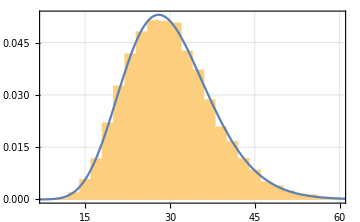

```mathematica
Show[Histogram[data,Automatic,PDF,PlotTheme->"Detailed"],Plot[PDF[ChiSquareDistribution[30],x],{x,0,80}],ImageSize->Medium]
```

Inverse Wishart distribution is the distribution of the inverse matrices from the Wishart distribution.

```mathematica
invdist=InverseWishartMatrixDistribution[30,Inverse[Σ]];
invmat=RandomVariate[invdist];
MatrixForm[invmat]
```

(0.0063379 | 0.00119924 | -0.00112327 | -0.0000537716 | 0.00376355
0.00119924 | 0.0121833 | -0.00189077 | -0.00246157 | 0.00528286
-0.00112327 | -0.00189077 | 0.0267855 | 0.00245515 | -0.0138271
-0.0000537716 | -0.00246157 | 0.00245515 | 0.00699219 | -0.0089418
0.00376355 | 0.00528286 | -0.0138271 | -0.0089418 | 0.063114)

Matrices from the Wishart distribution are symmetric and positive definite.

```mathematica
SymmetricMatrixQ[invmat]&&PositiveDefiniteMatrixQ[invmat]
```

True

Compare the distribution of eigenvalues for matrices from the Wishart and inverse Wishart distributions.

```mathematica
eigs=Flatten[RandomVariate[MatrixPropertyDistribution[Eigenvalues[x],x\[Distributed]dist],10^4]];
inveigs=Flatten[RandomVariate[MatrixPropertyDistribution[Eigenvalues[x]^-1,x\[Distributed]invdist],10^4]];
```

```mathematica
eigs
```

```mathematica
inveigs
```

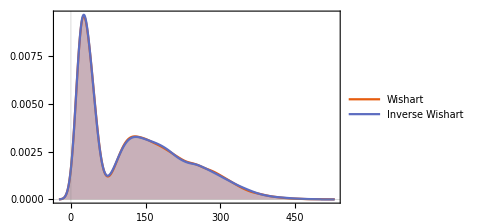

```mathematica
SmoothHistogram[{eigs,inveigs},PlotLegends->{"Wishart","Inverse Wishart"},Filling->Axis,ImageSize->Medium,PlotTheme->"Scientific"]
```